# Graph Colorings

Peter Burbery

Abstract

## Vertex Colorings

To color the vertices of a graph, no adjacent vertices can be the same color.

Make the function ColorGraphVertices a persistent function:

```mathematica
ResourceFunction["PersistResourceFunction"][{"PersistResourceFunction","ColorGraphVertices"}];
```

Color the vertices of the Petersen graph:

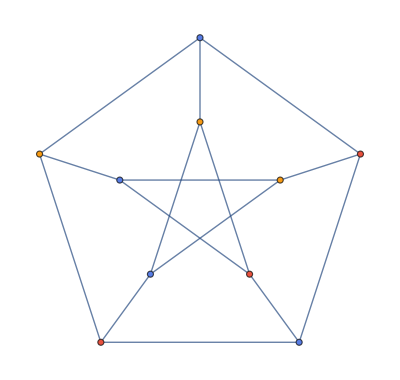

```mathematica
ColorGraphVertices[PetersenGraph[]]
```

Color the vertices of a random graph:

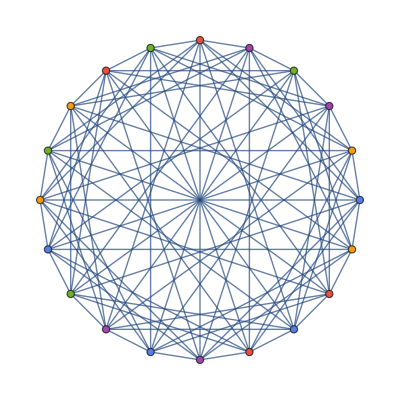

```mathematica
ColorGraphVertices[GraphData@@RandomSample[GraphData[],1]]
```

Make a gallery of graphs with colorings:

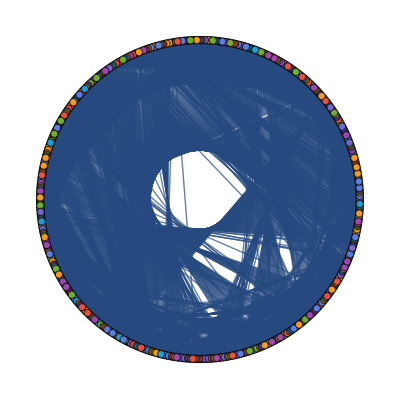
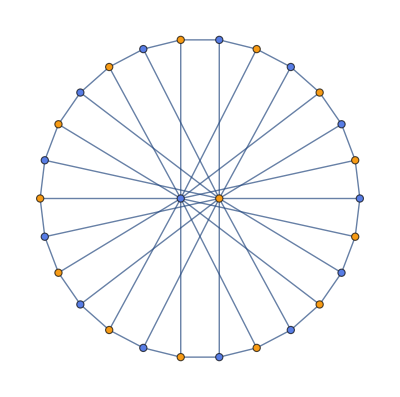
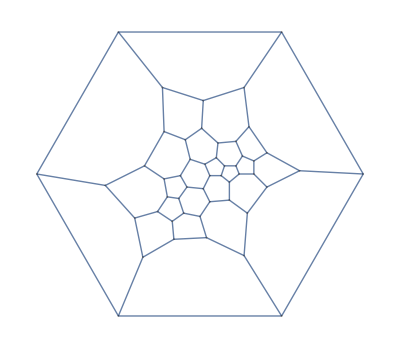
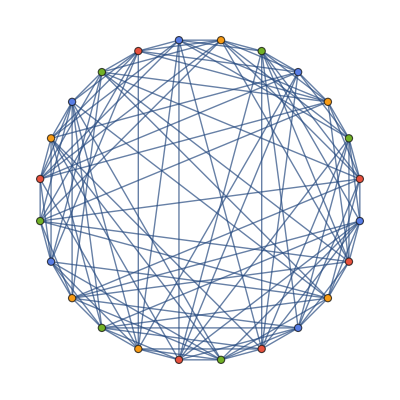
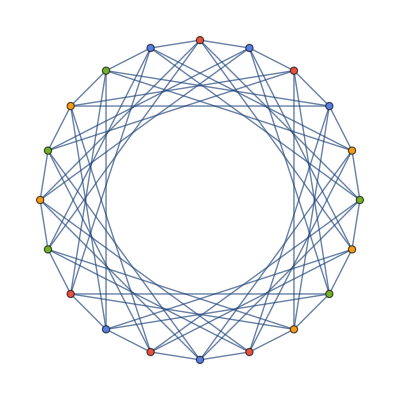
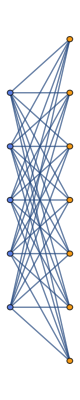
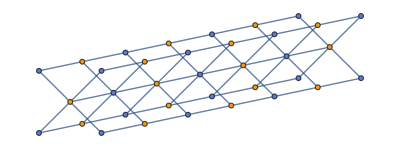
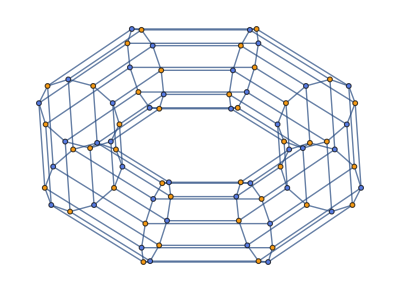

```mathematica
Select[GraphQ][ColorGraphVertices/@(GraphData/@RandomSample[GraphData[],10])]
```

Deploy a gallery of colorings to the web:

```mathematica
CloudDeploy[GalleryView[ColorGraphVertices/@(GraphData/@RandomSample[GraphData[],48])]]
```

FindVertexColoring::invc: Unable to find a coloring of the graph with less than 17 colors.

CloudObject[https://www.wolframcloud.com/obj/8685ca23-bb13-4147-b11a-900444f9cee1]

See information about the deployment:

```mathematica
CloudObjectInformation[CloudObject["https://www.wolframcloud.com/obj/8685ca23-bb13-4147-b11a-900444f9cee1"]]
```

CloudObject: 8685ca23-bb13-4147-b11a-900444f9cee1

## Edge Colorings

```mathematica
PersistResourceFunction[{"ColorGraphEdges"}]
```

{Success[…]}

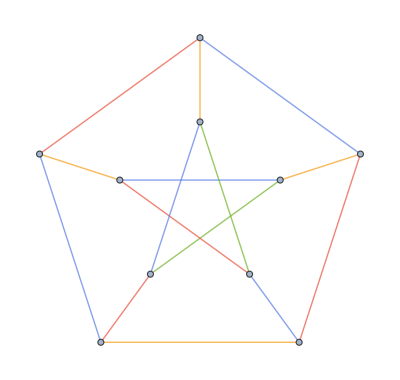

```mathematica
ColorGraphEdges[PetersenGraph[]]
```

Color the vertices of a random graph:

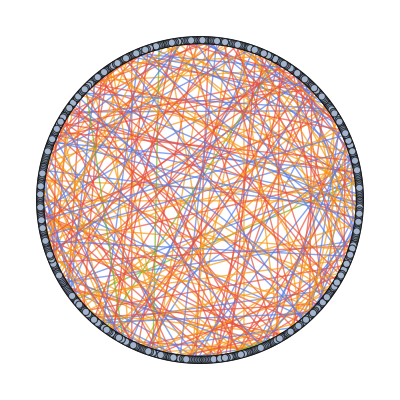

```mathematica
ColorGraphEdges[GraphData@@RandomSample[GraphData[],1]]
```

Make a gallery of graphs with colorings:

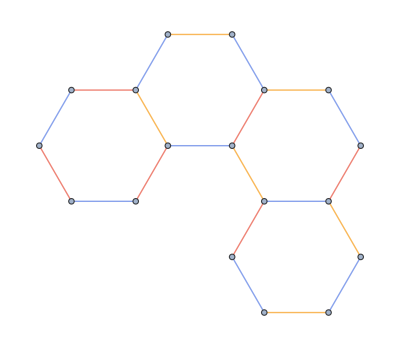
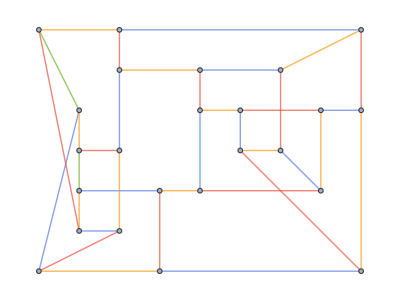
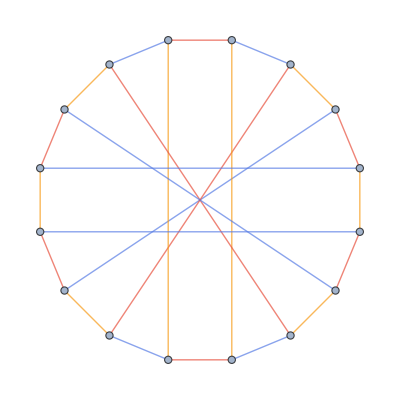
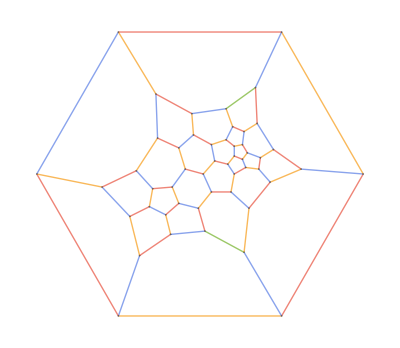
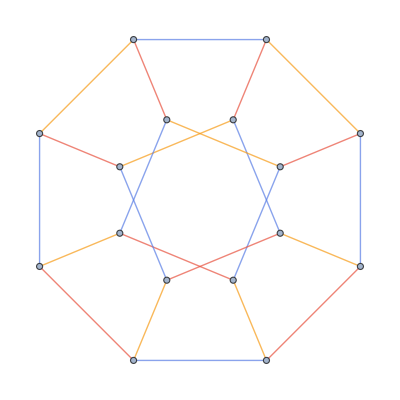
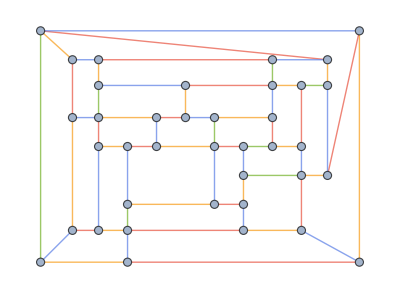
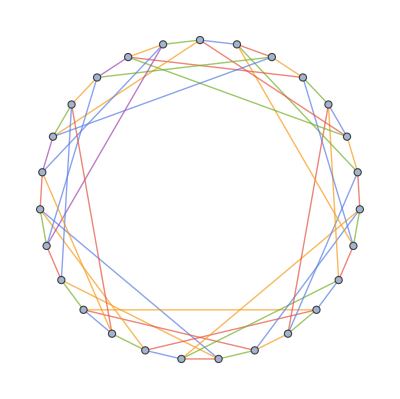
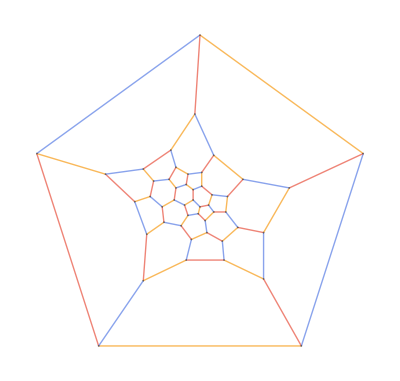

```mathematica
Select[GraphQ][ColorGraphEdges/@(GraphData/@RandomSample[GraphData[],10])]//Quiet
```